```mathematica
ClearAll["Global`*"];
ZD[x_,a_,b_]:=Piecewise[{
{1,x<a},
{0,x>b},
 {(b-x)/(b-a),And[x>=a , x<=b]}
}];
ND[x_, mu_, sigma_]:=Power[E, -Power[x-mu, 2]/(2*Power[sigma,2])];
SD[x_,a_,b_]:=Piecewise[{{0,x<a},{1,x>b}, {(x-a)/(b-a),And[x>a , x<b]}}];
```

# Funciones de pertenencia

## Temperatura de entrada

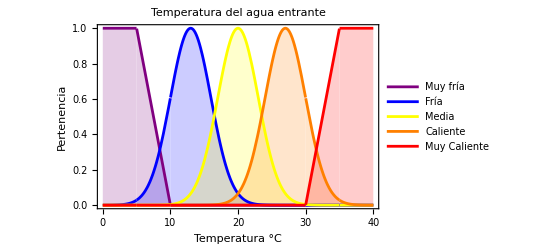

```mathematica
Sigma=3;
PSW= Plot[
{
ZD[t,5,10],
ND[t,13,Sigma],
ND[t,20,Sigma],
ND[t,27,Sigma],
SD[t, 30,35]
},{t,0,40},
PlotStyle->{Purple,Blue,Yellow,Orange,Red},
Filling->Bottom,
PlotLegends->{"Muy fría","Fría","Media","Caliente","Muy Caliente"},
PlotLabel->"Temperatura del agua entrante",
Frame->True,
FrameLabel->{"Temperatura °C", "Pertenencia"}
]
Export[FileNameJoin[{NotebookDirectory[],"SeawaterTemperature.png"}], PSW, ImageResolution->500];
```

## Temperatura del agua a evaporar

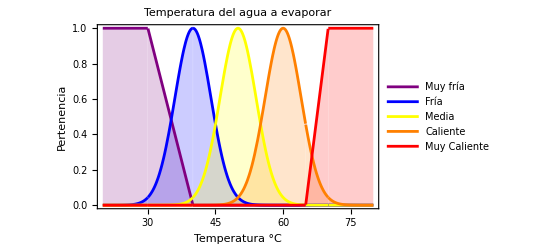

```mathematica
Sigma=4;
PHSW=Plot[
{
ZD[t,30,40],
ND[t,40,Sigma],
ND[t,50,Sigma],
ND[t,60,Sigma],
SD[t, 65,70]
},{t,20,80},
PlotStyle->{Purple,Blue,Yellow,Orange,Red},
Filling->Bottom,
PlotLegends->{"Muy fría","Fría","Media","Caliente","Muy Caliente"},
PlotLabel->"Temperatura del agua a evaporar",
FrameLabel->{"Temperatura °C", "Pertenencia"},
Frame->True
]
Export[FileNameJoin[{NotebookDirectory[],"HeatedSeawaterTemperature.png"}], PHSW, ImageResolution->500];
```

## Temperatura del recibidor solar

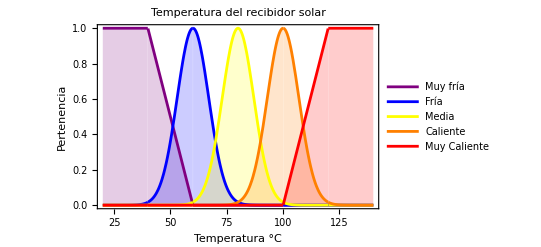

```mathematica
Sigma=7;
PSR=Plot[
{
ZD[t,40,60],
ND[t,60,Sigma],
ND[t,80,Sigma],
ND[t,100,Sigma],
SD[t, 100,120]
},{t,20,140},
PlotStyle->{Purple,Blue,Yellow,Orange,Red},
Filling->Bottom,
PlotLegends->{"Muy fría","Fría","Media","Caliente","Muy Caliente"},
PlotLabel->"Temperatura del recibidor solar",
Frame->True,
FrameLabel->{"Temperatura °C", "Pertenencia"}
]
Export[FileNameJoin[{NotebookDirectory[],"SolarReceiverTemperature.png"}], PSR, ImageResolution->500];
```

## Flujo de agua

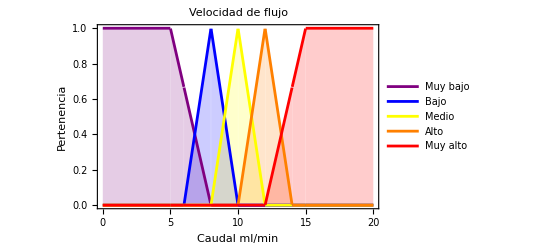

```mathematica
TD[x_,a_?Positive,b_?Positive ]:=Piecewise[{
{0,Or[x<a,x>b]},
{1-(2*Abs[x-(a+b)/2])/(b-a), True}
}];

PFV=Plot[
{
ZD[t,5,8],
TD[t,6,10],
TD[t,8,12],
TD[t,10,14],
SD[t, 12,15]
},{t,0,20},
PlotStyle->{Purple,Blue,Yellow,Orange,Red},
PlotRange->Full,
Filling->Bottom,
PlotLegends->{"Muy bajo","Bajo","Medio","Alto","Muy alto"},
PlotLabel->Style["Velocidad de flujo\n",Bold, Black],
Frame->True,
FrameLabel->{"Caudal ml/min", "Pertenencia"}
]
Export[FileNameJoin[{NotebookDirectory[],"FlowVelocity.png"}], PFV, ImageResolution->500];
```